```mathematica
SetDirectory[NotebookDirectory[]];
```

#### SiV+cavity data:

```mathematica
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*BF SiV*.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: BF SiV and cavity after installing interferometer after gas tuning1.txt

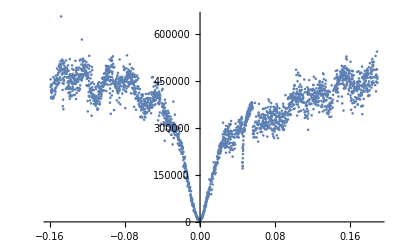

```mathematica
refspec=Import[names[[1]],"Table"];
xydata=Total[Partition[{refspec[[2;;,1]]-406.664,refspec[[2;;,9]]}ᵀ,1]ᵀ/1];trimxy=xydata/."NaN"-> Sequence[];mask=Length[#]>1&/@trimxy;xyreal=Complement[trimxy*Boole[mask],{{0}}][[2;;]];
ListPlot[xyreal]
```

```mathematica
Plot[(8971*Abs[t[x,406.66,.006,.033,0.0001,-.05,-7,0]]^2),{x,406.5,406.9},PlotRange->All]
```

-Graphics-

```mathematica
711-665
```

46

```mathematica
xyreal//Length
```

2398

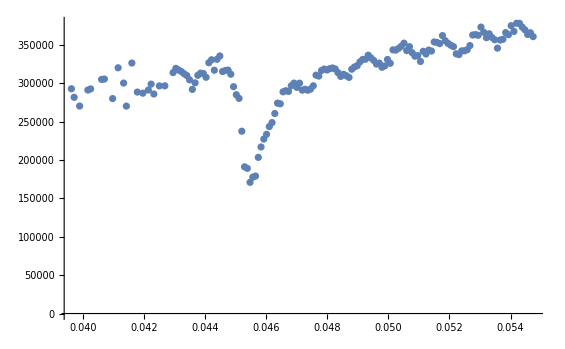

```mathematica
ListPlot[xyreal[[1350;;1500]]]
```

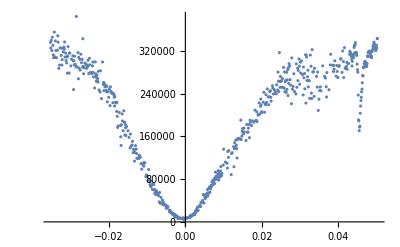

```mathematica
ListPlot[xyreal[[850;;1450]]]
```

```mathematica
r[ω_, ωa_, ωc_, g_, κ1_,κ2_, γ_] := 1-κ1/(ⅈ(ω-ωc)+κ2/2+g^2/(ⅈ(ω-ωa)+γ/2));
```

| Estimate | Standard Error | t-Statistic | P-Value
ωa | 0.454 | 1.49261×10^-8 | 3.04166×10^7 | 2.30138044187×10^-3623
ωc | 0.000443363 | 0.000111368 | 3.98107 | 0.0000771021
g | 0.0034072 | 0.000146106 | 23.3201 | 6.83161×10^-86
κ1 | 0.018035 | 0.000751409 | 24.0016 | 1.67143×10^-89
κ2 | 0.0321206 | 0.000659216 | 48.7254 | 1.11855×10^-209
γ | 0.000697976 | 0.000105236 | 6.63248 | 7.43283×10^-11
amp | 359493. | 3413.03 | 105.33 | 1.6536811096×10^-386

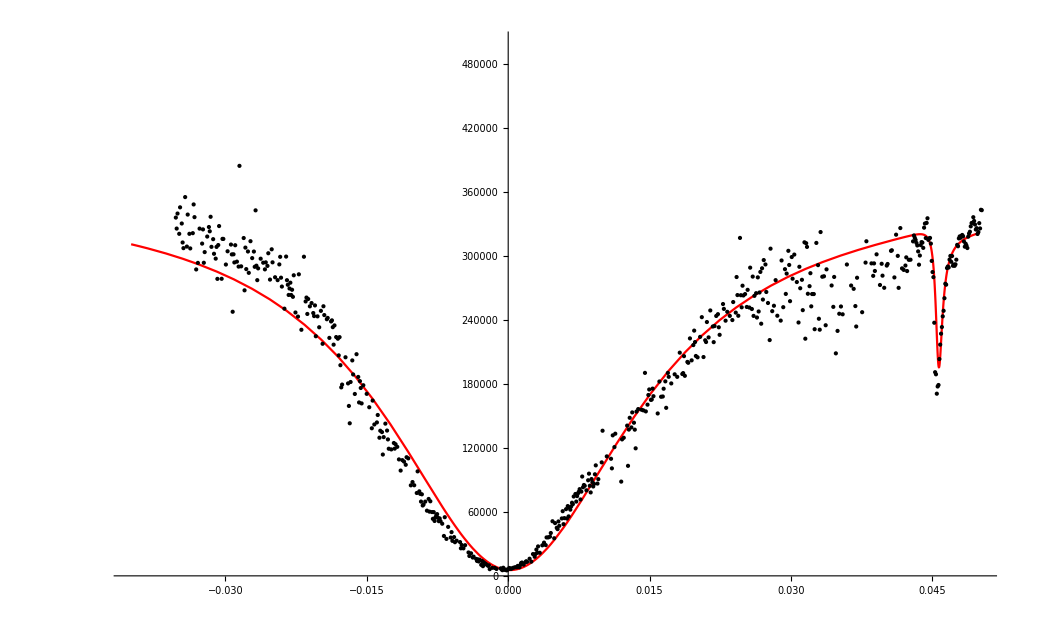

```mathematica
Cfit=NonlinearModelFit[xyreal[[850;;1450]],amp*(Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]])^2/.ωa-> 0.0454,{{ωa,0.454},{ωc,0},{g,.01},{κ1,0.01},{κ2,0.04},{γ,0.0001},{amp,450000}},ω];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,-0.04,0.05},Epilog->Point[xyreal[[850;;1450]]],PlotStyle->Red,PlotRange->{0,500000}]
```

| Estimate | Standard Error | t-Statistic | P-Value
ωa | 0.0454 | 2.06459×10^-7 | 219898. | 9.82337272177089×10^-612
ωc | 0.000077655 | 0.000232824 | 0.333535 | 0.739219
g | 0.01 | 1.996×10^-12 | 5.01002×10^9 | 7.12774181618443×10^-1235
κ1 | 0.0147231 | 1536.25 | 9.58377×10^-6 | 0.999992
κ2 | 0.0294462 | 0.00123615 | 23.8209 | 1.24179×10^-51
γ | 0.0001 | 0. | ∞ | 0.
amp | 342688. | 5889.74 | 58.1839 | 1.93812×10^-101

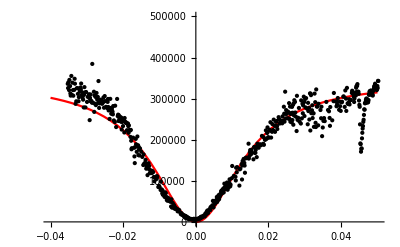

```mathematica
Cfit=NonlinearModelFit[Total[Partition[xyreal[[850;;1450]],binby]ᵀ/binby],amp*(Abs[r[ω,ωa,ωc,0,κ1,κ2,γ]])^2/.ωa-> 0.0454,{{ωa,0.0454},{ωc,0},{g,.01},{κ1,0.01},{κ2,0.04},{γ,0.0001},{amp,450000}},ω];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,-0.04,0.05},Epilog->Point[xyreal[[850;;1450]]],PlotStyle->Red,PlotRange->{0,500000}]
```

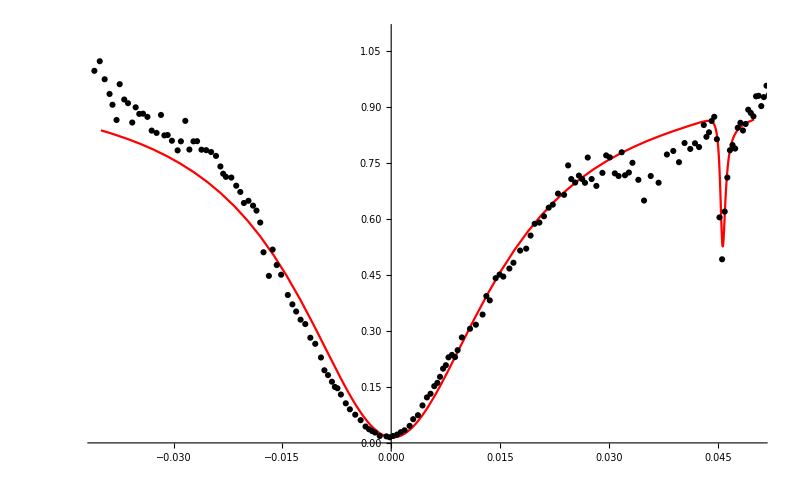

```mathematica
binby=4;
xybin=Total[Partition[xyreal,binby]ᵀ/binby];
Show[{Plot[Cfit[x]/370905,{x,-0.04,0.05},PlotStyle->Red,PlotRange-> {0,1.1}],ListPlot[(xybinᵀ*{1,1/370905})ᵀ,PlotStyle->Black]}]
```

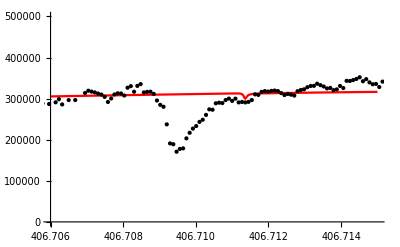

```mathematica
Plot[Cfit[x],{x,406.706,406.715},Epilog->Point[xyreal],PlotStyle->Red,PlotRange->{0,500000}]
```

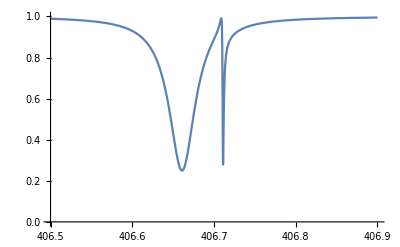

```mathematica
Plot[Abs[r[ω,406.709,406.663,0.01,0.01,0.04,0.0001]]^2,{ω,406.5,406.9}, PlotRange->{0,1}]
```

#### Bare cavity:

```mathematica
r[ω_, ωa_, ωc_, g_, κ1_,κ2_, γ_] := 1-κ1/(ⅈ(ω-ωc)+κ2/2+g^2/(ⅈ(ω-ωa)+γ/2));
```

```mathematica
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*reflection1.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: Cavity in reflection1.txt

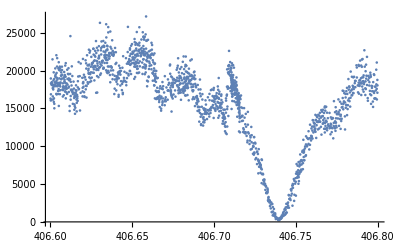

```mathematica
refspec=Import[names[[1]],"Table"];
xydata=Total[Partition[{refspec[[2;;,1]],refspec[[2;;,5]]}ᵀ,1]ᵀ/1];trimxy=xydata/."NaN"-> Sequence[];mask=Length[#]>1&/@trimxy;xyreal=Complement[trimxy*Boole[mask],{{0}}][[2;;]];
ListPlot[xyreal]
```

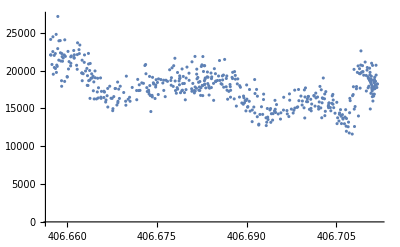

```mathematica
ListPlot[xyreal[[500;;1000]]]
```

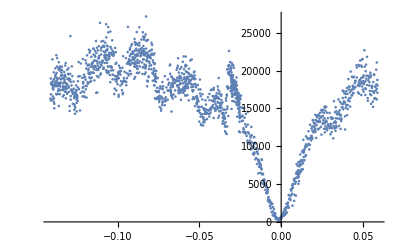

```mathematica
Cnorm={xyreal[[All,1]]-406.741,xyreal[[All,2]]}ᵀ;
ListPlot[Cnorm]
```

General::munfl: 0.398856^797.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0281779^797.5 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ωc | 0.0000850776 | 0.000193234 | 0.440282 | 0.659792
κ1 | 0.0139009 | 0.000481628 | 28.8624 | 9.83536×10^-148
κ2 | 0.0330766 | 0.000674621 | 49.03 | 1.149×10^-320
α | 0.1 | 0. | ∞ | 0.
ϕ | 0. | 0. | ComplexInfinity | 0.
amp | 20060.1 | 85.5289 | 234.542 | 0.

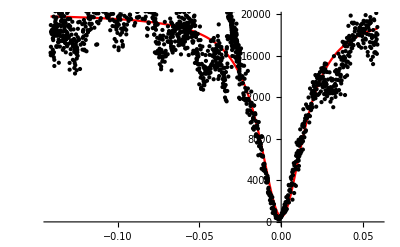

```mathematica
Cfit=NonlinearModelFit[Cnorm,amp*Abs[r[ω, ωa, ωc, g, κ1,κ2, γ]]^2/.{g-> 0,γ-> 0.0001,ωa-> 0},{{ωc,-0.01},{κ1,0.01},{κ2, 0.04},{α,0.1},{ϕ,0},{amp,20000}},ω];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,Cfit["Data"][[1,1]],Cfit["Data"][[-1,1]]},Epilog->Point[Cfit["Data"]],PlotStyle->Red]
```

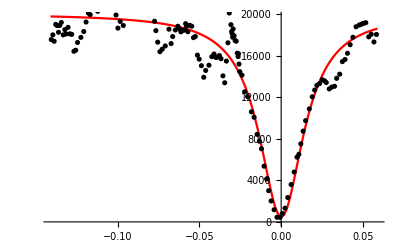

```mathematica
binby=10;
xybin=Total[Partition[Cnorm,binby]ᵀ/binby];
Show[{Plot[Cfit[x],{x,Cfit["Data"][[1,1]],Cfit["Data"][[-1,1]]},PlotStyle->Red],ListPlot[xybin,PlotStyle->Black]}]
```

```mathematica
fitκ1 = κ1/.Cfit["BestFitParameters"];
fitκ2 = κ2/.Cfit["BestFitParameters"];
fitCamp = amp/.Cfit["BestFitParameters"];
```

#### SiV on resonance

```mathematica
SetDirectory[NotebookDirectory[]];
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*PLE*image.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: 14.45.08_Pulse Experiment_Two laser PLE_ID8_image.txt

2: 13.20.05_Pulse Experiment_SiV PLE  on resonance_ID1_image.txt

3: 10.50.18_Pulse Experiment_1laser PLE  1Mcts , NO green_ID5_image.txt

4: 15.27.58_Pulse Experiment_PLE SiV dn_ID7_image.txt

5: 15.29.50_Pulse Experiment_PLE SiV up_ID8_image.txt

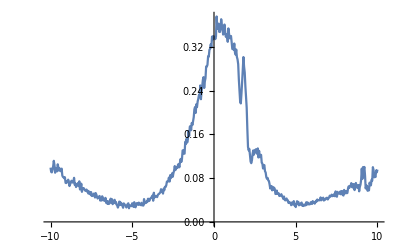

```mathematica
data=Import[#,"Table"]&/@names;
XYdata=Total[Partition[{data[[2,All,1]],data[[2,All,2]]}ᵀ,1]ᵀ/1];
ListLinePlot[XYdata]
```

```mathematica
Rnorm={XYdata[[All,1]]/1000,XYdata[[All,2]]}ᵀ;
```

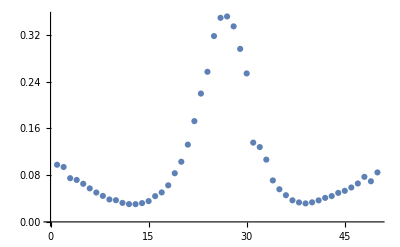

```mathematica
ListPlot[Total[Partition[XYdata[[All,2]],10]ᵀ/10]]
```

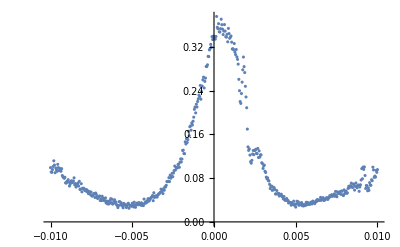

```mathematica
ListPlot[Rnorm]
```

```mathematica
r[ω_, ωa_, ωc_, g_, κ1_,κ2_, γ_] := 1-κ1/(ⅈ(ω-ωc)+κ2/2+g^2/(ⅈ(ω-ωa)+γ/2));
```

General::munfl: 0.00861567^247.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0138948^247.5 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ωa | 0.000473287 | 0.0000126583 | 37.3894 | 2.7652×10^-146
ωc | -0.0000914041 | 0.0000721211 | -1.26737 | 0.205619
g | 0.00520891 | 0.0000218257 | 238.66 | 0.
α | 0.1 | 0. | ∞ | 0.
ϕ | 0. | 0. | ComplexInfinity | 0.
amp | 0.386504 | 0.00206213 | 187.429 | 0.

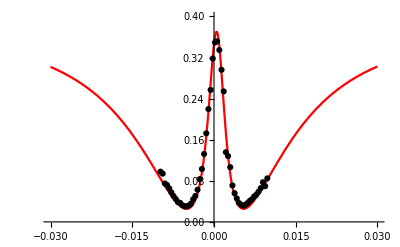

```mathematica
Rfit=NonlinearModelFit[Rnorm,amp*Abs[r[ω, ωa, ωc, g, κ1,κ2, γ]]^2/.{κ1-> fitκ1,κ2-> fitκ2,γ-> 0.0001},{{ωa,0},{ωc,0},{g,0.006},{α,0.1},{ϕ,0},{amp,1}},ω];
Rfit["ParameterTable"]
binby=10;
Rxybin=Total[Partition[Rnorm,binby]ᵀ/binby];
Show[{Plot[Rfit[x],{x,-.03,.03},PlotStyle->Red,PlotRange->{0,0.4}],ListPlot[Rxybin,PlotStyle->Black]}]
```

```mathematica
fitg = g/.Rfit["BestFitParameters"];
fitRamp = amp/.Rfit["BestFitParameters"];
```

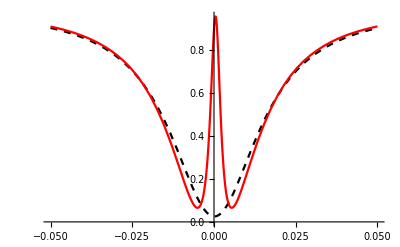

```mathematica
Plot[{Cfit[x]/fitCamp,Rfit[x]/fitRamp},{x,-.05,.05},PlotStyle->{Directive[Black,Dashed],Red}]
```

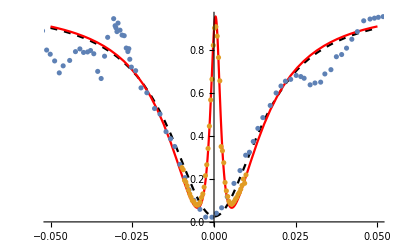

```mathematica
Show[{Plot[{Cfit[x]/fitCamp,Rfit[x]/fitRamp},{x,-.05,.05},PlotStyle->{Directive[Black,Dashed],Red},AxesOrigin-> -.05],ListPlot[{(xybinᵀ*{1,1/fitCamp})ᵀ,(Rxybinᵀ*{1,1/fitRamp})ᵀ}]}]
```

```mathematica
(4*fitg^2)/(fitκ2*0.0001)
```

32.812

```mathematica
Rfit[0]/fitRamp
```

0.896499

#### Cavity half-detuned

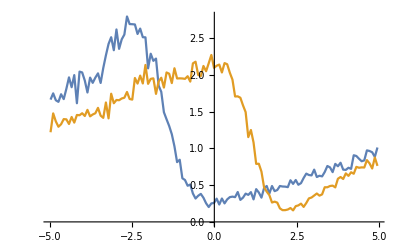

```mathematica
rawdn=Total[Partition[{data[[4,All,1]],data[[4,All,2]]}ᵀ,4]ᵀ/4];
rawup=Total[Partition[{data[[5,All,1]],data[[5,All,2]]}ᵀ,4]ᵀ/4];
XYdatadn={rawdn[[All,1]],rawdn[[All,2]]}ᵀ;
XYdataup={rawup[[All,1]],rawup[[All,2]]}ᵀ;
ListLinePlot[{XYdatadn,XYdataup}]
```

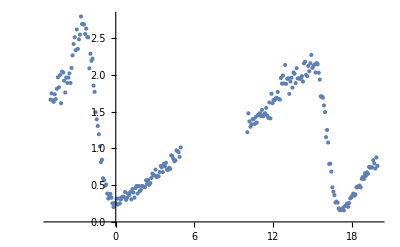

```mathematica
ListPlot[Flatten[{XYdatadn,(XYdataupᵀ+{15,0})ᵀ},1]]
```

```mathematica
JointFit=NonlinearModelFit[Flatten[{XYdatadn,(XYdataupᵀ+{15,0})ᵀ},1],If[ω<7,amp1*Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2,amp2*Abs[r[ω-15,ωa2,ωc,g2,κ1,κ2,γ]]^2]/.{κ1-> fitκ1*1000,κ2-> fitκ2*1000,γ-> 0.1},{{g1,fitg*1000},{g2,fitg*1000},{ωa1,-2.5},{ωa2,-0.2},{ωc,-12},{amp1,2.5},{amp2,2}},ω]
JointFit["ParameterTable"]
```

FittedModel[If[ω<7,2.50233 Abs[r[ω,«5»,0.1]]^2,2.3413 Abs[r[ω-15,-0.111325,-13.7539,«18»,«19»,33.0766,0.1]]^2]]

| Estimate | Standard Error | t-Statistic | P-Value
g1 | 5.95235 | 0.0938689 | 63.4113 | 3.54648×10^-153
g2 | 6.14912 | 0.0846089 | 72.677 | 7.52861×10^-167
ωa1 | -2.49002 | 0.0335231 | -74.2778 | 4.74366×10^-169
ωa2 | -0.111325 | 0.0352251 | -3.1604 | 0.0017755
ωc | -13.7539 | 0.273427 | -50.3019 | 1.80211×10^-130
amp1 | 2.50233 | 0.0296885 | 84.2862 | 6.81716×10^-182
amp2 | 2.3413 | 0.0279556 | 83.7506 | 3.04775×10^-181

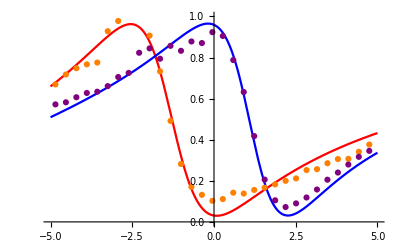

```mathematica
Show[{Plot[{Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2/.Join[{κ1-> fitκ1*1000,κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]],Abs[r[ω,ωa2,ωc,g2,κ1,κ2,γ]]^2/.Join[{κ1-> fitκ1*1000,κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]]},{ω,-5,5},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{(Dxybinᵀ*{1,1/amp1/.JointFit["BestFitParameters"]})ᵀ,(Uxybinᵀ*{1,1/amp2/.JointFit["BestFitParameters"]})ᵀ},PlotStyle->{Orange,Purple}]}]
```

```mathematica
barecavity[x_]:=(B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.Ufit["BestFitParameters"] )/.{g->0,κ-> 33.1,γ-> 0.1}
```

```mathematica
FindMaximum[Abs[barecavity[x]-Ufit[x]]/barecavity[x],{x,0}]
```

{0.617586,{x→-0.607249}}

```mathematica
FindMaximum[Abs[barecavity[x]-Ufit[x]]/barecavity[x],{x,2}]
```

{0.92228,{x→2.32682}}

```mathematica
0.65+0.36
```

1.01

```mathematica
diff2[x_]:=((B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.Ufit["BestFitParameters"] )- (B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.Dfit["BestFitParameters"] ))/.{g-> 5.27,κ-> 33.1,γ-> 0.1}
```

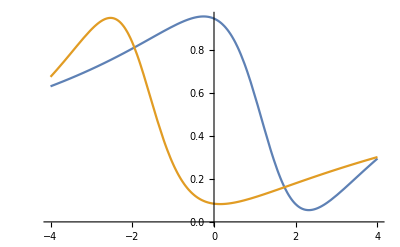

```mathematica
Plot[{(B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.Ufit["BestFitParameters"] )/.{g-> 5.27,κ-> 33.1,γ-> 0.1},(B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.Dfit["BestFitParameters"] )/.{g-> 5.27,κ-> 33.1,γ-> 0.1}},{x,-4,4}]
```

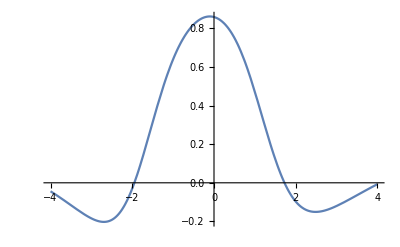

```mathematica
Plot[diff2[x],{x,-4,4}]
```

```mathematica
FindMaximum[Ufit[x],x]
FindMinimum[Ufit[x],x]
```

{0.953479,{x→-0.256344}}

{0.0546813,{x→2.31941}}

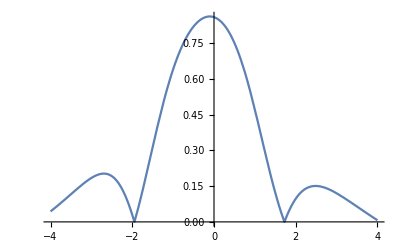

```mathematica
Plot[Abs[Ufit[x]-Dfit[x]],{x,-4,4}]
```

```mathematica
FindMaximum[Abs[Dfit[x]-Ufit[x]],x]
```

{0.862231,{x→-0.103661}}

```mathematica
8/33.
```

0.242424

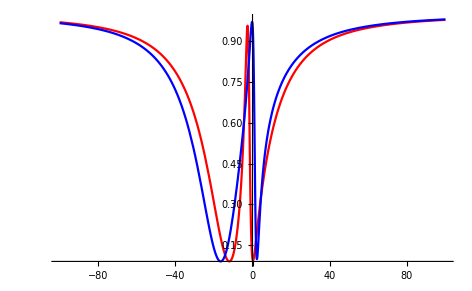

```mathematica
Plot[{Dfit[x],Ufit[x]},{x,-100,100},PlotStyle->{Red,Blue}]
```

#### Few kappa detuned

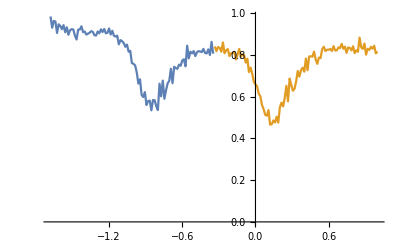

```mathematica
XYdataS=Total[Partition[{data[[3,All,1]],(data[[3,All,2]])/(Max[data[[3,All,2]]])}ᵀ,1]ᵀ/1];
ListLinePlot[{XYdataS[[100;;200]],XYdataS[[201;;]]},AxesOrigin->0]
```

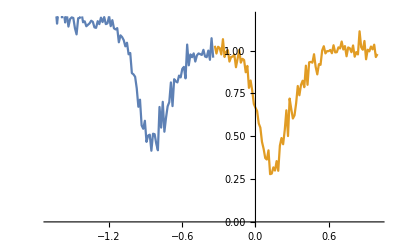

```mathematica
XYdataS=Total[Partition[{data[[3,All,1]],2*(data[[3,All,2]]-Mean[data[[3,All,2]]])/(Max[data[[3,All,2]]])+1}ᵀ,1]ᵀ/1];
ListLinePlot[{XYdataS[[100;;200]],XYdataS[[201;;]]},AxesOrigin->0,PlotRange->{0,1.2}]
```

```mathematica
XYdataSup=XYdataS[[100;;200]];
XYdataSdn=XYdataS[[201;;]];
```

| Estimate | Standard Error | t-Statistic | P-Value
ωa | -15720.5 | 5.02194×10^10 | -3.13037×10^-7 | 1.
ωc | 35.8935 | 5642.94 | 0.00636078 | 0.994938

| Estimate | Standard Error | t-Statistic | P-Value
ωa | -1.6379 | 0.421851 | -3.88265 | 0.000186539
ωc | 11.9877 | 11.4464 | 1.04729 | 0.297517

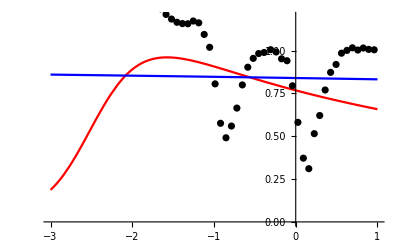

```mathematica
SDfit=NonlinearModelFit[XYdataSdn,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> 5.27,κ1->23.2,κ2->33.1,γ-> 0.1},{{ωa,-0.3},{ωc,-20}},ω];
SUfit=NonlinearModelFit[XYdataSup,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> 5.27,κ1->23.2,κ2->33.1,γ-> 0.1},{{ωa,-1.3},{ωc,-20}},ω];
SDfit["ParameterTable"]
SUfit["ParameterTable"]
binby=5;
SDxybin=Total[Partition[XYdataSdn,binby]ᵀ/binby];
SUxybin=Total[Partition[XYdataSup,binby]ᵀ/binby];
Show[{Plot[{SUfit[x],SDfit[x]},{x,-3,1},PlotStyle->{Red,Blue},PlotRange->{0,1.2}],ListPlot[{SDxybin,SUxybin},PlotStyle->Black]}]
```

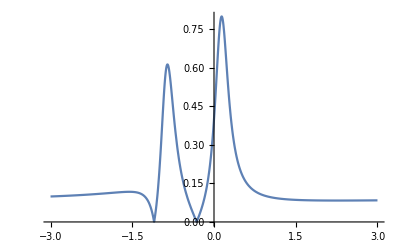

```mathematica
Plot[Abs[SUfit[x]-SDfit[x]],{x,-3,3},PlotRange->All]
```

```mathematica
diff[x_]:=Abs[SUfit[x]-SDfit[x]]
```

```mathematica
FindMaximum[diff[x],x]
```

{0.800769,{x→0.140491}}

```mathematica
34*1/(1+4*(0.25)^2)
```

27.2

```mathematica
√(38./(1+4(2)^2)*33*0.1)
```

2.71597

Expected transmission dip:  T~1/(1+C)^2

```mathematica
1-1./((1+38/(1+4(2)^2))^2)
```

0.904463

```mathematica
1-1./((1+38/(1+4(0.5)^2))^2)
```

0.9975

```mathematica
1-1./((1+38/(1+4(0)^2))^2)
```

0.999343

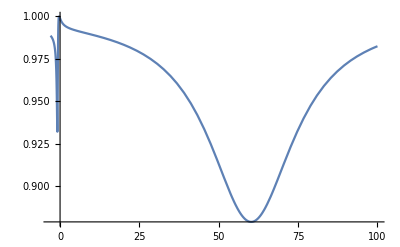

```mathematica
Plot[1-Abs[t[x,-0.3,5.6,33,0.1,60,0,0]]^2,{x,-3,100},PlotRange->All]
```

```mathematica
FindMinimum[1-Abs[t[x,-0.3,5.6,33,0.1,60,0,0]]^2,{x,-1}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.931863,{x→-0.849376}}

```mathematica
(1-0.93)/(1-0.87)
```

0.538462

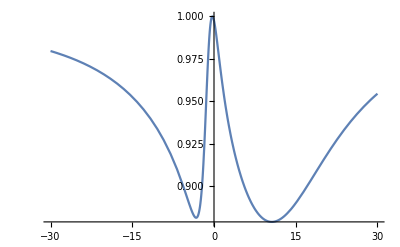

```mathematica
Plot[1-Abs[t[x,-0.3,5.6,33,0.1,8,0,0]]^2,{x,-30,30},PlotRange->All]
```

```mathematica
FindMinimum[1-Abs[t[x,-0.3,5.6,33,0.1,8,0,0]]^2,{x,-1}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.88143,{x→-3.27509}}

```mathematica
FindMinimum[1-Abs[t[x,-0.3,5.6,33,0.1,8,0,0]]^2,{x,10}]
```

{0.878982,{x→10.6068}}

```mathematica
(1-0.8814)/(1-0.8790)
```

0.980165

```mathematica
1/0.6
```

1.66667

```mathematica
Series[((1+c)*c - 4 x^2)/((1+c)^2-4 x^2),{c,∞,3}]
```

1-1/c+(1/c)^2+(-1-4 x^2)/c^3+O[1/c]^4

```mathematica
Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{ω-> ωa}
```

```mathematica
Abs[1-κ1/((2 g^2)/γ+κ2/2+ⅈ (ωa-ωc))]^2//FullSimplify
```

Abs[1-(2 γ κ1)/(4 g^2+γ (κ2+2 ⅈ (ωa-ωc)))]^2

```mathematica
(1/(1-x^2)-(1+c)/((1+c)^2-x^2))//FullSimplify
```

(c (1+c+x^2))/((-1+x^2) (-(1+c)^2+x^2))

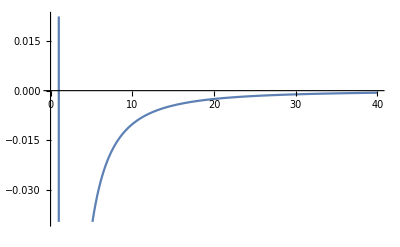

```mathematica
Plot[1/(1-x^2)/.c-> 50,{x,0,40}]
```

```mathematica
Rfit[0]/fitRamp
Cfit[0]/fitCamp
```

0.896499

0.0254566

```mathematica
Rfit[0]/fitRamp - Cfit[0]/fitCamp
```

0.871042

```mathematica
coop = (4*fitg^2)/(fitκ2*0.0001)
```

32.812

```mathematica
.5((4fitκ1)/fitκ1 coop/(1+coop))/(1-(2fitκ1)/fitκ1)^2
```

1.94085

```mathematica
(1-(2fitκ1)/fitκ2)^2
```

0.0254308

```mathematica
(4fitκ1)/fitκ2
```

1.68106

```mathematica
(Abs[r[1000,0,0,fitg,fitκ1,fitκ1,0.0001]]^2-Abs[r[0,0,0,0,fitκ1,fitκ1,0.0001]]^2)/Abs[r[1000,0,0,0,fitκ1,fitκ1,0.0001]]^2
```

0.

```mathematica
Abs[r[0,0,0,fitg,fitκ1,fitκ1,0.0001]]^2
Abs[r[0,0,0,0,fitκ1,fitκ1,0.0001]]^2
```

0.950055

1.

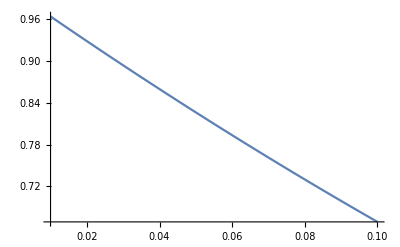

```mathematica
Plot[Abs[r[0,0,0,fitg,x,fitκ1,0.0001]]^2,{x,0.01,0.1}]
```

```mathematica
Abs[r[0,0,0,0,fitκ1,2fitκ1,0.0001]]^2
Abs[r[0,0,0,fitg,fitκ1,2fitκ1,0.0001]]^2
(Abs[r[0,0,0,fitg,fitκ1,2fitκ1,0.0001]]^2-Abs[r[0,0,0,0,fitκ1,2fitκ1,0.0001]]^2)/Abs[r[0,0,0,0,fitκ1,2fitκ1,0.0001]]^2
```

0.

0.95067

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
(coop/(1+36))/(1+coop/(1+36))
```

0.470005

```mathematica
Abs[r[0,fitg^2/(2*fitκ2),2*fitκ2,0,fitκ1,fitκ2,0.0001]]^2
Abs[r[0,fitg^2/(2*fitκ2),2*fitκ2,fitg,fitκ1,fitκ2,0.0001]]^2
(Abs[r[0,fitg^2/(2*fitκ2),2*fitκ2,fitg,fitκ1,fitκ2,0.0001]]^2-Abs[r[0,fitg^2/(2*fitκ2),0,2*fitκ2,fitκ1,fitκ2,0.0001]]^2)/(Abs[r[0,fitg^2/(2*fitκ2),0,2*fitκ2,fitκ1,fitκ2,0.0001]]^2)
```

0.942672

0.18812

-0.811819

```mathematica
effcoop[x_]:=(coop/(1+(2x)^2))/(coop/(1+(2x)^2)+1)
```

```mathematica
effcoop[10]
```

0.0756365

```mathematica
actcont[x_]:=-(Abs[r[0,fitg^2/(x*fitκ2),x*fitκ2,fitg,fitκ1,fitκ2,0.0001]]^2-Abs[r[0,fitg^2/(x*fitκ2),0,x*fitκ2,fitκ1,fitκ2,0.0001]]^2)/(Abs[r[0,fitg^2/(x*fitκ2),0,x*fitκ2,fitκ1,fitκ2,0.0001]]^2)
```

```mathematica
actcont[10]
```

0.125185

```mathematica
actcont[10]/effcoop[10]
```

1.65509

```mathematica
4*fitκ1/fitκ2
```

1.68106

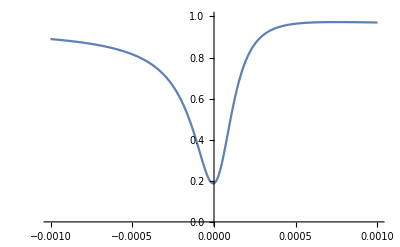

```mathematica
Plot[Abs[r[x,fitg^2/(2*fitκ2),2*fitκ2,fitg,fitκ1,fitκ2,0.0001]]^2,{x,-0.001,0.001},PlotRange->{0,1}]
```

```mathematica
1/(0.00044/fitg^2)
```

0.0616654

```mathematica
2*fitκ2
```

0.0661533

```mathematica
(coop(1+coop+36))/((1+coop)^2-36)
```

2.06879

```mathematica
1-(4*k1)/k2*1/(1+c)+(4*k1^2)/k2^2*1/(1+c)^2 -(1-(4*k1)/k2+(4*k1^2)/k2^2)//FullSimplify
```

(4 c k1 (-(2+c) k1+k2+c k2))/((1+c)^2 k2^2)

```mathematica
1/(1+ⅈ*x)+1/(1-ⅈ*x)//FullSimplify
```

2/(1+x^2)